# Aggressive Early Deflation

Working through Braman, Byers and Mathias. SIMA JMat Analysis 2002 MultiShift Part 2

## Opening Example

This is the example form the paper with larger subdiagonal entries and some randomization

```mathematica
m=6; ϵ=0.1; γ=0.1
A=Chop[Normal[SparseArray[ {
Band[{1,1}]->{6,1,2,3,4,5},
Band[{1,1},{1,m},{0,1}]->{6,5,4,3,2,1},
Band[{2,1}]->γ},
{m,m}]]+ϵ UpperTriangularize[RandomReal[{-1,1},{m,m}]]];
MatrixForm[A]
Dia={6,5,4,3,2,1};
TableForm[{λ=Eigenvalues[A],Abs[λ-Dia]/Dia}ᵀ,
TableHeadings->{Dia,{"λ","(λ-Dia⟦i⟧)/Dia⟦i⟧"}}]
```

0.1

(5.91415 | 5.07184 | 3.95094 | 2.98349 | 1.97121 | 0.975113
0.1 | 0.916761 | -0.0716649 | 0.0468759 | 0.0632073 | 0.0905849
0 | 0.1 | 2.06202 | 0.0436267 | 0.0749687 | 0.0612702
0 | 0 | 0.1 | 2.98641 | 0.0962702 | 0.0569112
0 | 0 | 0 | 0.1 | 3.90406 | 0.063191
0 | 0 | 0 | 0 | 0.1 | 5.09581)

| λ | (λ-Dia⟦i⟧)/Dia⟦i⟧
6 | 6.0156 | 0.00259971
5 | 5.10134 | 0.0202681
4 | 3.90907 | 0.0227323
3 | 2.97985 | 0.00671547
2 | 2.04424 | 0.0221175
1 | 0.829107 | 0.170893

I should be able to “spike” this from the bottom and the top!

### Double Spike and Back

Spiking and unspiking the matrix is easy!

```mathematica
m=Length[A];
{Q,H}=SchurDecomposition[A⟦2;;5,2;;5⟧];
BigQ=IdentityMatrix[m]; BigQ⟦2;;5,2;;5⟧=Q;
QtAQ =Chop[BigQᵀ.A.BigQ];
{QBack,H}=HessenbergDecomposition[QtAQ⟦1;;6,1;;6⟧];
BigQBack=IdentityMatrix[m]; BigQBack⟦1;;6,1;;6⟧=QBack;
QBtAQB =Chop[BigQBackᵀ.QtAQ.BigQBack];
TabView[{
"Spike"->MatrixPlot[QtAQ,ColorRules->{0->Green}],
"Back"->MatrixPlot[QBtAQB,ColorRules->{0->Green}],
"Original"->MatrixPlot[A,ColorRules->{0->Green}]
}]
```

123

### Embedded Double Spike and Back Real Form

Spiking and unspiking the matrix is easy!

```mathematica
{m,n1,n2}={16,4,10};SpId=IdentityMatrix[m,SparseArray];
H=Chop[HessenbergDecomposition[RandomReal[{-1,1},{m,m}]]⟦2⟧];
InRange=n1+1;;n2;
OutRange=n1;;n2;
Q1=Q2=SpId; 
{Q1⟦InRange,InRange⟧,WeeH}=SchurDecomposition[H⟦InRange,InRange⟧];
S = Chop[Q1ᵀ.H.Q1];
Q2⟦OutRange,OutRange⟧ =HessenbergDecomposition[S⟦OutRange,OutRange⟧]⟦1⟧;
B=Chop[Q2ᵀ.S.Q2];
TabView[{
"Spikes"->MatrixPlot[S,ColorRules->{0->LightGreen},Mesh->{{n1,n2},{n1,n2}}],
"Back"->MatrixPlot[B,ColorRules->{0->LightGreen},Mesh->{{n1,n2},{n1,n2}}],
"Original"->MatrixPlot[H,ColorRules->{0->LightGreen},Mesh->{{n1,n2},{n1,n2}}],
"Q1"->MatrixPlot[Q1,ColorRules->{0->LightGreen},Mesh->{{n1,n2},{n1,n2}}],
"Q2"->MatrixPlot[Q2,ColorRules->{0->LightGreen},Mesh->{{n1,n2},{n1,n2}}]
}]
```

12345

```mathematica
m=Length[A];
{Q,H}=SchurDecomposition[A⟦3;;4,3;;4⟧];
BigQ=IdentityMatrix[m]; BigQ⟦3;;4,3;;4⟧=Q;
QtAQ =Chop[BigQᵀ.A.BigQ];
{QBack,H}=HessenbergDecomposition[QtAQ⟦2;;5,2;;5⟧];
BigQBack=IdentityMatrix[m]; BigQBack⟦2;;5,2;;5⟧=QBack;
QBtAQB =Chop[BigQBackᵀ.QtAQ.BigQBack];

TabView[{
MatrixPlot[QtAQ,ColorRules->{0->Green}],
MatrixPlot[QBtAQB,ColorRules->{0->Green}],
MatrixPlot[A,ColorRules->{0->Green}]
}]
```

123

```mathematica
Map[MatrixForm,{QtAQ,QBtAQB,A}]
```

{(6.04172 | 4.95579 | -3.67353 | -3.42229 | 1.92099 | 0.998982
0.1 | 0.996942 | -0.0507243 | 0.0419078 | 0.0506798 | -0.0595048
0 | -0.0995341 | 1.96321 | -0.179284 | 0.0541183 | -0.0698223
0 | -0.00964211 | 0 | 2.98782 | 0.0919969 | 0.0322272
0 | 0 | 0.00964211 | -0.0995341 | 4.0983 | -0.0109721
0 | 0 | 0 | 0 | 0.1 | 5.09032),(6.04172 | 4.95579 | 3.9864 | 3.05214 | 1.92099 | 0.998982
0.1 | 0.996942 | 0.0464472 | -0.0466035 | 0.0506798 | -0.0595048
0 | 0.1 | 1.95553 | -0.0792839 | -0.0627366 | 0.0663896
0 | 0 | 0.1 | 2.9955 | -0.0863501 | -0.0388094
0 | 0 | 0 | 0.1 | 4.0983 | -0.0109721
0 | 0 | 0 | 0 | 0.1 | 5.09032),(6.04172 | 4.95579 | 3.9864 | 3.05214 | 1.92099 | 0.998982
0.1 | 0.996942 | 0.0464472 | -0.0466035 | 0.0506798 | -0.0595048
0 | 0.1 | 1.95553 | -0.0792839 | -0.0627366 | 0.0663896
0 | 0 | 0.1 | 2.9955 | -0.0863501 | -0.0388094
0 | 0 | 0 | 0.1 | 4.0983 | -0.0109721
0 | 0 | 0 | 0 | 0.1 | 5.09032)}

```mathematica
H
```

{{0.968081,-0.0387985,0.00721039,-0.00487112,-0.033511},{0.1,1.90894,-0.0890419,0.0239881,0.0884181},{0.,0.1,3.09137,0.000841665,0.0793677},{0.,0.,0.1,3.92414,0.0420196},{0.,0.,0.,0.1,4.97047}}

```mathematica
H
```

{{0.968081,-0.0387985,0.00721039,-0.00487112,-0.033511},{0.1,1.90894,-0.0890419,0.0239881,0.0884181},{0.,0.1,3.09137,0.000841665,0.0793677},{0.,0.,0.1,3.92414,0.0420196},{0.,0.,0.,0.1,4.97047}}

### Embedded Double Spike and Back Complex Form

Spiking and unspiking complex matrices works the same way!

```mathematica
{m,n1,n2}={16,4,10};SpId=IdentityMatrix[m,SparseArray];
H=Chop[HessenbergDecomposition[RandomComplex[{-1-I,1+I},{m,m}]]⟦2⟧];
InRange=n1+1;;n2;
OutRange=n1;;n2;
Q1=Q2=SpId; 
{Q1⟦InRange,InRange⟧,WeeH}=SchurDecomposition[H⟦InRange,InRange⟧];
S = Chop[ConjugateTranspose[Q1].H.Q1];
Q2⟦OutRange,OutRange⟧ =HessenbergDecomposition[S⟦OutRange,OutRange⟧]⟦1⟧;
B=Chop[ConjugateTranspose[Q2].S.Q2];
TabView[{
"Spikes"->MatrixPlot[S,ColorRules->{0->LightGreen},Mesh->{{n1,n2},{n1,n2}}],
"Back"->MatrixPlot[B,ColorRules->{0->LightGreen},Mesh->{{n1,n2},{n1,n2}}],
"Original"->MatrixPlot[H,ColorRules->{0->LightGreen},Mesh->{{n1,n2},{n1,n2}}],
"Q1"->MatrixPlot[Q1,ColorRules->{0->LightGreen},Mesh->{{n1,n2},{n1,n2}}],
"Q2"->MatrixPlot[Q2,ColorRules->{0->LightGreen},Mesh->{{n1,n2},{n1,n2}}]
}]
```

12345

```mathematica
m=Length[A];
{Q,H}=SchurDecomposition[A⟦3;;4,3;;4⟧];
BigQ=IdentityMatrix[m]; BigQ⟦3;;4,3;;4⟧=Q;
QtAQ =Chop[BigQᵀ.A.BigQ];
{QBack,H}=HessenbergDecomposition[QtAQ⟦2;;5,2;;5⟧];
BigQBack=IdentityMatrix[m]; BigQBack⟦2;;5,2;;5⟧=QBack;
QBtAQB =Chop[BigQBackᵀ.QtAQ.BigQBack];

TabView[{
MatrixPlot[QtAQ,ColorRules->{0->Green}],
MatrixPlot[QBtAQB,ColorRules->{0->Green}],
MatrixPlot[A,ColorRules->{0->Green}]
}]
```

123

```mathematica
Map[MatrixForm,{QtAQ,QBtAQB,A}]
```

{(6.04172 | 4.95579 | -3.67353 | -3.42229 | 1.92099 | 0.998982
0.1 | 0.996942 | -0.0507243 | 0.0419078 | 0.0506798 | -0.0595048
0 | -0.0995341 | 1.96321 | -0.179284 | 0.0541183 | -0.0698223
0 | -0.00964211 | 0 | 2.98782 | 0.0919969 | 0.0322272
0 | 0 | 0.00964211 | -0.0995341 | 4.0983 | -0.0109721
0 | 0 | 0 | 0 | 0.1 | 5.09032),(6.04172 | 4.95579 | 3.9864 | 3.05214 | 1.92099 | 0.998982
0.1 | 0.996942 | 0.0464472 | -0.0466035 | 0.0506798 | -0.0595048
0 | 0.1 | 1.95553 | -0.0792839 | -0.0627366 | 0.0663896
0 | 0 | 0.1 | 2.9955 | -0.0863501 | -0.0388094
0 | 0 | 0 | 0.1 | 4.0983 | -0.0109721
0 | 0 | 0 | 0 | 0.1 | 5.09032),(6.04172 | 4.95579 | 3.9864 | 3.05214 | 1.92099 | 0.998982
0.1 | 0.996942 | 0.0464472 | -0.0466035 | 0.0506798 | -0.0595048
0 | 0.1 | 1.95553 | -0.0792839 | -0.0627366 | 0.0663896
0 | 0 | 0.1 | 2.9955 | -0.0863501 | -0.0388094
0 | 0 | 0 | 0.1 | 4.0983 | -0.0109721
0 | 0 | 0 | 0 | 0.1 | 5.09032)}

```mathematica
H
```

{{0.968081,-0.0387985,0.00721039,-0.00487112,-0.033511},{0.1,1.90894,-0.0890419,0.0239881,0.0884181},{0.,0.1,3.09137,0.000841665,0.0793677},{0.,0.,0.1,3.92414,0.0420196},{0.,0.,0.,0.1,4.97047}}

```mathematica
H
```

{{0.968081,-0.0387985,0.00721039,-0.00487112,-0.033511},{0.1,1.90894,-0.0890419,0.0239881,0.0884181},{0.,0.1,3.09137,0.000841665,0.0793677},{0.,0.,0.1,3.92414,0.0420196},{0.,0.,0.,0.1,4.97047}}

### Random Double Spike To Hessenberg Complex Form

Does this still work on a “Spike” Matrix that did not come from a Hessenberg Matrix?  Of course it doesn’t! It wipes out the upper spike and changes the lower spike. The story is that in the double spike case the spikes “match” in an appropriate sense.  I may try to work out what that sense is. Right now I do not know what it is.

```mathematica
{m,n1,n2}={16,4,10};SpId=IdentityMatrix[m,SparseArray];
H=Chop[HessenbergDecomposition[RandomComplex[{-1-I,1+I},{m,m}]]⟦2⟧];
InRange=n1+1;;n2;
OutRange=n1;;n2;
Q1=Q2=SpId; 
{Q1⟦InRange,InRange⟧,WeeH}=SchurDecomposition[H⟦InRange,InRange⟧];
OldS = Chop[ConjugateTranspose[Q1].H.Q1];
NewS=OldS;
(* Messing with the Spikes *)
NewS⟦n1;;n2,n1⟧+=RandomComplex[{-1-I,1+I},1+n2-n1];
NewS⟦n2+1,n1+1;;n2⟧+=RandomComplex[{-1-I,1+I},n2-n1];
(* Hessenberging  the Spikes *)
Q2⟦OutRange,OutRange⟧ =HessenbergDecomposition[NewS⟦OutRange,OutRange⟧]⟦1⟧;
B=Chop[ConjugateTranspose[Q2].NewS.Q2];
TabView[{
"H-Spikes"->MatrixPlot[OldS,ColorRules->{0->LightGreen},Mesh->{{n1,n2},{n1,n2}}],
"Spikes"->MatrixPlot[NewS,ColorRules->{0->LightGreen},Mesh->{{n1,n2},{n1,n2}}],
"Back"->MatrixPlot[B,ColorRules->{0->LightGreen},Mesh->{{n1,n2},{n1,n2}}]
}]
```

123

I should be able to do this in the other direction.  Lets check

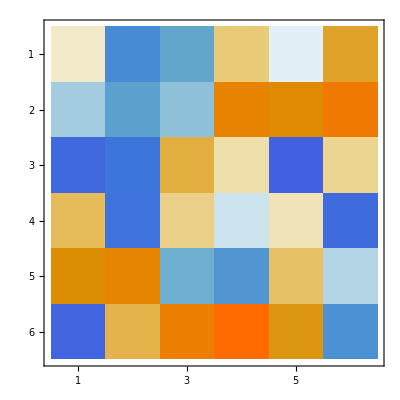
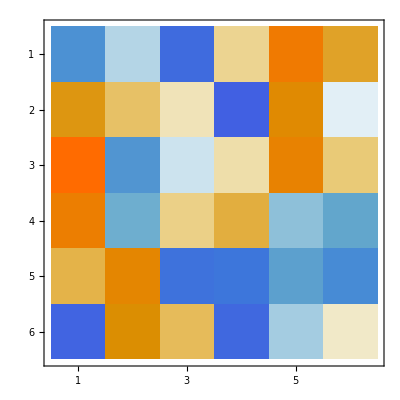

```mathematica
Map[MatrixPlot,{J.Aᵀ.J,A}]
```

{1.32019×10^-15,3.32837}

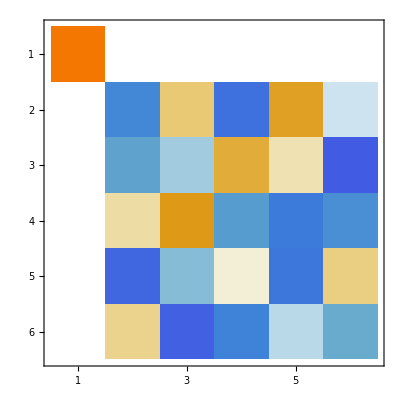
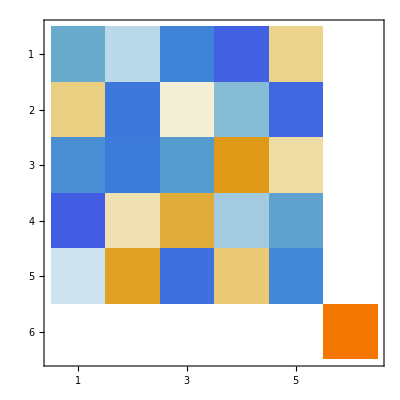

```mathematica
m=6;
A=RandomReal[{-1,1},{m,m}];
J=Reverse[IdentityMatrix[m,SparseArray]];
{Q1,H1}=HessenbergDecomposition[A];
{Q2,H2}=HessenbergDecomposition[J.Aᵀ.J];
Map[Norm,{A-Q1.H1.Q1ᵀ, A-Q2.H2.Q2ᵀ}]
Map[MatrixPlot,{Q1,J.Q1.J}]
```

```mathematica
{m,n1,n2}={16,4,10};SpId=IdentityMatrix[m,SparseArray];
H=Chop[HessenbergDecomposition[RandomComplex[{-1-I,1+I},{m,m}]]⟦2⟧];
InRange=n1+1;;n2;
OutRange=n1;;n2;
Q1=Q2=SpId; 
{Q1⟦InRange,InRange⟧,WeeH}=SchurDecomposition[H⟦InRange,InRange⟧];
OldS = Chop[ConjugateTranspose[Q1].H.Q1];
NewS=OldS;
(* Messing with the Spikes *)
NewS⟦n1;;n2,n1⟧+=RandomComplex[{-1-I,1+I},1+n2-n1];
NewS⟦n2+1,n1+1;;n2⟧+=RandomComplex[{-1-I,1+I},n2-n1];
(* Hessenberging  the Spikes *)
Q2⟦OutRange,OutRange⟧ =HessenbergDecomposition[NewS⟦OutRange,OutRange⟧]⟦1⟧;
B=Chop[ConjugateTranspose[Q2].NewS.Q2];
TabView[{
"H-Spikes"->MatrixPlot[OldS,ColorRules->{0->LightGreen},Mesh->{{n1,n2},{n1,n2}}],
"Spikes"->MatrixPlot[NewS,ColorRules->{0->LightGreen},Mesh->{{n1,n2},{n1,n2}}],
"Back"->MatrixPlot[B,ColorRules->{0->LightGreen},Mesh->{{n1,n2},{n1,n2}}]
}]
```

123

I can move the spike further pretty easily

```mathematica
{m,n1,n2}={16,4,10};SpId=IdentityMatrix[m,SparseArray];
H=Chop[HessenbergDecomposition[RandomComplex[{-1-I,1+I},{m,m}]]⟦2⟧];
InRange=n1+1;;n2;
OutRange=n1;;n2+1;
Q1=Q2=SpId; 
{Q1⟦InRange,InRange⟧,WeeH}=SchurDecomposition[H⟦InRange,InRange⟧];
OldS = Chop[ConjugateTranspose[Q1].H.Q1];
NewS=OldS;
(* Messing with the Spikes *)
NewS⟦n1;;n2,n1⟧+=RandomComplex[{-1-I,1+I},1+n2-n1];
NewS⟦n2+1,n1+1;;n2⟧+=RandomComplex[{-1-I,1+I},n2-n1];
(* Hessenberging  the Spikes *)
Q2⟦OutRange,OutRange⟧ =HessenbergDecomposition[NewS⟦OutRange,OutRange⟧]⟦1⟧;
B=Chop[ConjugateTranspose[Q2].NewS.Q2];
TabView[{
"H-Spikes"->MatrixPlot[OldS,ColorRules->{0->LightGreen},Mesh->{{n1,n2},{n1,n2}}],
"Spikes"->MatrixPlot[NewS,ColorRules->{0->LightGreen},Mesh->{{n1,n2},{n1,n2}}],
"Back"->MatrixPlot[B,ColorRules->{0->LightGreen},Mesh->{{n1,n2},{n1,n2}}]
}]
```

123

### Chasing Double Spike Matrices

OK since H⟺Double Spike aka Frame
There is a way to chase Double Spikes through the loop.  Is there a way to do it directly

```mathematica
m=Length[A];
{Q,H}=SchurDecomposition[A⟦3;;4,3;;4⟧];
BigQ=IdentityMatrix[m]; BigQ⟦3;;4,3;;4⟧=Q;
QtAQ =Chop[BigQᵀ.A.BigQ];
{QBack,H}=HessenbergDecomposition[QtAQ⟦2;;5,2;;5⟧];
BigQBack=IdentityMatrix[m]; BigQBack⟦2;;5,2;;5⟧=QBack;
QBtAQB =Chop[BigQBackᵀ.QtAQ.BigQBack];

TabView[{
MatrixPlot[QtAQ,ColorRules->{0->Green}],
MatrixPlot[QBtAQB,ColorRules->{0->Green}],
MatrixPlot[A,ColorRules->{0->Green}]
}]
```

123

## Hessenberg Plus Spike Discussion “Bottom” p950

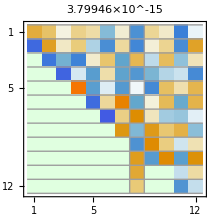
I can “Schur” the bottom k×k block of a Hessenberg matrix.  It makes a vertical spike. 
	Ĥ=-Graphics-
The spike is in the -(k+1)=n-k-1 column.  I am going to think of the spike as rooted in the on the diagonal. With this understanding the spike is Ĥ⟦-(k+1);;-1, -(k+1)⟧. The observation from the paper is that the bottom entries of this spike can be tiny even if the original Hessenberg form is not nearly reducible by traditional standards.  Schur decomposition seems to naturally grade the spike so that small entries are near the bottom.  As long as the lower block is reasonably sized the “real” schur form does not seem to cause many issues.

#### Demo

```mathematica
{n,k}={12,4};
H=HessenbergDecomposition[RandomReal[{-1,1},{n,n}]]⟦2⟧;
H33=H⟦-k;;-1,-k;;-1⟧;
{Q,T}=SchurDecomposition[H33];
QBig=IdentityMatrix[n]; QBig⟦-k;;-1,-k;;-1⟧=Q;
QBtHQB=Chop[QBigᵀ.H.QBig];
TabView[{
"Q_Bigᵀ.H.Q_Big"->MatrixPlot[QBtHQB,PlotLabel->Norm[H33-Q.T.Qᵀ],
ColorRules->{0->LightGreen},
Mesh->{All,{n-k-1,n-k}}],
"V-Spike"->ListPlot[QBtHQB⟦All,n-k⟧],
"H"->MatrixPlot[Chop[H]]
}]
```

123

## Hessenberg Plus Spike Discussion Top

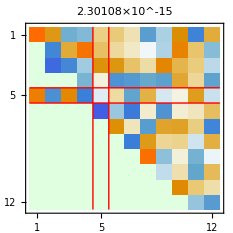
I can “Schur” the top k×k block of a Hessenberg matrix.  It makes a horizontal spike. 
	Ĥ=-Graphics-
The spike is in row k+1 .  I am going to think of the spike as rooted on the diagonal. With this understanding the spike is Ĥ⟦k+1, 1;;k+1⟧. Just like the column spikes the last entries of this spike can be tiny even if the original Hessenberg form is not nearly reducible by traditional standards.  Schur decomposition seems to naturally grade the spike so that small entries are near the bottom.  As long as the selected block is reasonably sized the “real” schur form does not seem to cause many issues.

#### Demo

```mathematica
{n,k}={32,9};
H=HessenbergDecomposition[RandomReal[{-1,1},{n,n}]]⟦2⟧;
H11=H⟦1;;k,1;;k⟧;
{Q,T}=SchurDecomposition[H11];
QBig=IdentityMatrix[n]; QBig⟦1;;k,1;;k⟧=Q;
QBtHQB=Chop[QBigᵀ.H.QBig];
Spike=0*H; Spike⟦{k+1},1;;k+1⟧=QBtHQB⟦{k+1},1;;k+1⟧;
TabView[{
"Q_Bigᵀ.H.Q_Big"->MatrixPlot[QBtHQB,PlotLabel->Norm[H11-Q.T.Qᵀ],
ColorRules->{0->LightGreen},MeshStyle->Red,
Mesh->{{k,k+1},{k,k+1}}],
"H-Spike"->MatrixPlot[Spike, PlotLegends->Automatic,MeshStyle->Red,
Mesh->{{k,k+1},{k,k+1}}],
"H"->MatrixPlot[Chop[H]]
}]
```

123

## Hessenberg Plus Double Spike Discussion

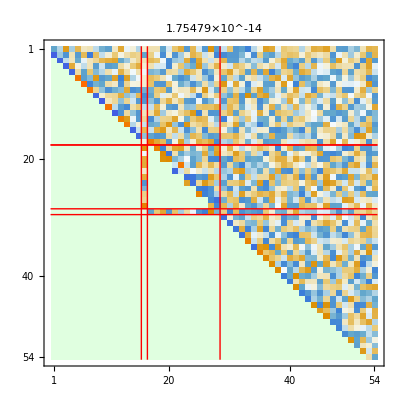
If do the same process in the middle we get two spikes that frame a central Schur form.  I am going to describe this with an m_1 for the start of a k×k Schur decomposition.  The spikes “frame” the reduced block
	Ĥ=-Graphics-

### Demo

```mathematica
{n,m1,k}={54,17,11};
H=HessenbergDecomposition[RandomReal[{-1,1},{n,n}]]⟦2⟧;
H22=H⟦m1;;m1+k,m1;;m1+k⟧;
{Q,T}=SchurDecomposition[H22];
QBig=IdentityMatrix[n]; QBig⟦m1;;m1+k,m1;;m1+k⟧=Q;
QBtHQB=QBigᵀ.H.QBig;
MatrixPlot[Chop[QBtHQB],PlotLabel->Norm[H22-Q.T.Qᵀ],ColorRules->{0->LightGreen},
MeshStyle->Red,
Mesh->{{m1,m1,m1+k,m1+k+1},{m1-2,m1-1,m1+k}}]
```

-Graphics-

```mathematica
TabView[{
"Q_Bigᵀ.H.Q_Big"->MatrixPlot[
Chop[QBtHQB],PlotLabel->Norm[H22-Q.T.Qᵀ],ColorRules->{0->LightGreen},
MeshStyle->Red,
Mesh->{{m1,m1,m1+k,m1+k+1},{m1-2,m1-1,m1+k}}],
"V and H Spikes"->ListPlot[
{QBtHQB⟦All,n1⟧,QBtHQB⟦n2+1,All⟧},
PlotRange->All,Joined->True,Mesh->All],
"H"->MatrixPlot[Chop[H]]
}]
```

123

## Attempt at: Spike Form ⟺ Hessenberg Form A) Found Something funny!

The paper discusses Spike  ⇒ Hessenberg.  There has to be a natural way to go the other way. 
The simple “high-level” way I thought about this (doing a Hessenberg on the expanded Spike form) was wrong but produced something possibly useful. I can rip a element of the sub diagonal and move it well of the diagonal! This might be useful for a splitting it most certainly concentrates all the crap into a single number.  If the number is zero then we have split the matrix in a sort of divide and conquer mechanism.

I am doing this in the complex form because it only works “just right” in the real case if the bottom diagonal is a singleton.

I am not sure if this is useful. IT does mean there is one thing to try to make small rather than a collection of things (the tail of the spike) to try to make small.

#### Demo: Trailing Dot Effect. Complex Triangular Schur Form!

Here is the complex arithmetic version for a initial H.

```mathematica
{n,k}={32,9};
H=HessenbergDecomposition[RandomReal[{-1,1},{n,n}]]⟦2⟧;
H11=H⟦1;;k,1;;k⟧;
{Q,T}=SchurDecomposition[H11,RealBlockDiagonalForm->False];
QBig=IdentityMatrix[n]; QBig⟦1;;k,1;;k⟧=Q;
QBtHQB=Chop[ConjugateTranspose[QBig].H.QBig];
{QBack,HBack}=HessenbergDecomposition[QBtHQB⟦1;;k+1,1;;k+1⟧];
QBackBig=IdentityMatrix[n]; QBackBig⟦1;;k+1,1;;k+1⟧=ConjugateTranspose[QBack];
Print[Norm[QBackBig.ConjugateTranspose[QBackBig]-IdentityMatrix[n]]]
HBackBig=Chop[QBackBig.QBtHQB.ConjugateTranspose[QBackBig]];
TabView[{
"HBackBig"->MatrixPlot[HBackBig,
ColorRules->{0->LightGreen},MeshStyle->Red,
Mesh->{{k,k+1,k+2},{1,2,k,k+1}}],
"Q_Bigᵀ.H.Q_Big"->MatrixPlot[QBtHQB,
ColorRules->{0->LightGreen},MeshStyle->Red,
Mesh->{{k,k+1,k+2},{1,2,k,k+1}}],
"H"->MatrixPlot[Chop[H],ColorRules->{0->LightGreen},MeshStyle->Red,
Mesh->{{k,k+1,k+2},{1,2,k,k+1}}]
}]
```

1.19717×10^-15

123

#### Demo: Trailing Dot Effect. Real Pseudo-Triangular Schur Form!

Here is the real arithmetic version for a initial H. It produces a singleton provided the last eigenvalue in the Schur form is real i.e. the last entry is not part of a 2×2 block.

```mathematica
{n,k}={32,9};
H=HessenbergDecomposition[RandomReal[{-1,1},{n,n}]]⟦2⟧;
H11=H⟦1;;k,1;;k⟧;
{Q,T}=SchurDecomposition[H11,RealBlockDiagonalForm->True];
QBig=IdentityMatrix[n]; QBig⟦1;;k,1;;k⟧=Q;
QBtHQB=Chop[Transpose[QBig].H.QBig];
{QBack,HBack}=HessenbergDecomposition[QBtHQB⟦1;;k+1,1;;k+1⟧];
QBackBig=IdentityMatrix[n]; QBackBig⟦1;;k+1,1;;k+1⟧=Transpose[QBack];
Print[Norm[QBackBig.Transpose[QBackBig]-IdentityMatrix[n]]]
HBackBig=Chop[QBackBig.QBtHQB.Transpose[QBackBig]];
TabView[{
"HBackBig"->MatrixPlot[HBackBig,
ColorRules->{0->LightGreen},MeshStyle->Red,
Mesh->{{k,k+1,k+2},{1,2,k,k+1}}],
"Q_Bigᵀ.H.Q_Big"->MatrixPlot[QBtHQB,
ColorRules->{0->LightGreen},MeshStyle->Red,
Mesh->{{k,k+1,k+2},{1,2,k,k+1}}],
"H"->MatrixPlot[Chop[H],ColorRules->{0->LightGreen},MeshStyle->Red,
Mesh->{{k,k+1,k+2},{1,2,k,k+1}}]
}]
```

7.76886×10^-16

123

#### Demo: Double Trailing Dot Effect. Diagonal Schur Form!

Here is the real arithmetic version for a initial H. It produces a singleton provided the last eigenvalue in the Schur form is real i.e. the last entry is not part of a 2×2 block.

```mathematica
{n,n1, k}={32,11,9};
H=HessenbergDecomposition[RandomReal[{-1,1},{n,n}]]⟦2⟧;
rr1=n1;;n1+k;
rr2=rr1;
H22=H⟦rr1,rr2⟧;
{Q,T}=SchurDecomposition[H22,RealBlockDiagonalForm->False];
QBig=IdentityMatrix[n]; QBig⟦rr1,rr2⟧=Q;
QBtHQB=ConjugateTranspose[QBig].H.QBig;
{QBack,HBack}=HessenbergDecomposition[QBtHQB⟦rr1,rr2⟧];
QBackBig=IdentityMatrix[n]; QBackBig⟦rr1,rr2⟧=ConjugateTranspose[QBack];
HBackBig=Chop[QBackBig.QBtHQB.ConjugateTranspose[QBackBig]];
TabView[{
"HBackBig"->MatrixPlot[HBackBig,
ColorRules->{0->LightGreen},MeshStyle->Red,
Mesh->{{n1,n1+k},{n1,n1+k}}],
"Q_Bigᵀ.H.Q_Big"->MatrixPlot[Chop[QBtHQB],
ColorRules->{0->LightGreen},MeshStyle->Red,
Mesh->{{n1,n1+k},{n1,n1+k}}],
"H"->MatrixPlot[Chop[H],ColorRules->{0->LightGreen},MeshStyle->Red,
Mesh->{{n1,n1+k},{n1,n1+k}}]
}]
```